```mathematica
Integrate[1/theta*(R/theta)^(k-1)*Exp[-R/theta]/Gamma[k]*(4/3*Pi*R^3*nu)*3/Sqrt[2]*Pi*BesselJ[3/2,q*t*R]/(q*t*R)^(3/2),{R,0,Infinity},Assumptions->k>1&&theta>0&&q*t>0]
```

1/(q^3 t^3)4 nu π^(3/2) (1+q^2 t^2 theta^2)^(-1/2-k/2) (-k q t theta Cos[(1+k) ArcTan[q t theta]]+√(1+q^2 t^2 theta^2) Sin[k ArcTan[q t theta]])

```mathematica
FullSimplify[Convolve[UnitBox[x/W1]/(2*W1),Exp[-x^2/(2*sigma^2)]/(√(π/2) sigma),x,y],Assumptions->W1≥0]
```

(Erf[(W1-2 y)/(2 √2 sigma)]+Erf[(W1+2 y)/(2 √2 sigma)])/(2 W1)

```mathematica
Integrate[1/(2*W1)* (Erf[(W1-2 y)/(2 √2 sigma)]+Erf[(W1+2 y)/(2 √2 sigma)]),{y,-Infinity,Infinity},Assumptions->sigma>0]
```

1

```mathematica
SmoothedBox[y_,sigma_]:=1/(2*W1)* (Erf[(W1-2 y)/(2 √2 sigma)]+Erf[(W1+2 y)/(2 √2 sigma)])
```

```mathematica
CForm[SmoothedBox[x,SIGMA]]
```

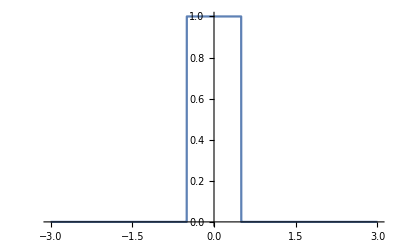

```mathematica
Plot[SmoothedBox[x,10^(-10)],{x,-3,3},PlotRange->All]
```

```mathematica
Integrate[FullSimplify[Convolve[UnitBox[x/W1],UnitBox[x/W2],x,y,Assumptions->a>0],Assumptions->sigma>0&&W1>0&&W2>0],{y,-Infinity,Infinity},Assumptions->W1>0&&W2>0]
```

Piecewise[{{W1 W2, (W1-W2>0&&W1>0&&W2>0)||(W1-W2<0&&W1>0)}, {W2^2, True}}]

```mathematica
FullSimplify[Convolve[UnitBox[y/W1],UnitBox[y/W2],y,x,Assumptions->a>0],Assumptions->sigma>0&&W1>0&&W2>0&&Element[x,Reals]&&x!=0]
```

Piecewise[{{W1, W1<W2+2 x&&W1+2 x<W2}, {W2, W1≥W2+2 x&&W1+2 x≥W2}, {1/2 (W1+W2-2 x), (W1≥W2||W1+2 x≥W2)&&(W1<W2||W1<W2+2 x)&&W1+W2>2 x}, {(W1+W2)/2+x, W1+W2+2 x>0&&((W1==W2&&W1>W2+2 x)||(W1≥W2+2 x&&W1<W2)||(W1>W2&&W1+2 x<W2))}, {0, True}}]

```mathematica
FullSimplify[Convolve[Convolve[UnitBox[x/a],UnitBox[x/b],x,y,Assumptions->a>0],Exp[-y^2/(2*sigma^2)]/(√(2 π) sigma),y,x,Assumptions->sigma>0],Assumptions->sigma>0&&a>0&&b>0]
```

Piecewise[{{1/4 (2 (ⅇ^(-(a+b-2 x)^2/(8 sigma^2))-ⅇ^(-(a-b+2 x)^2/(8 sigma^2))-ⅇ^(-(-a+b+2 x)^2/(8 sigma^2))+ⅇ^(-(a+b+2 x)^2/(8 sigma^2))) √(2/π) sigma-(a+b-2 x) Erf[(a-b-2 x)/(2 √2 sigma)]+(a+b-2 x) Erf[(a+b-2 x)/(2 √2 sigma)]+(-a+b-2 x) Erf[(a-b+2 x)/(2 √2 sigma)]-2 b Erf[(-a+b+2 x)/(2 √2 sigma)]+(a+b+2 x) Erf[(a+b+2 x)/(2 √2 sigma)]), a>b}, {(ⅇ^(-(b+x)^2/(2 sigma^2)) (1+ⅇ^((2 b x)/sigma^2)-2 ⅇ^((b (b+2 x))/(2 sigma^2))) sigma)/(√(2 π))+1/2 ((b-x) Erf[(b-x)/(√2 sigma)]-2 x Erf[x/(√2 sigma)]+(b+x) Erf[(b+x)/(√2 sigma)]), a==b}, {1/4 (2 (ⅇ^(-(a+b-2 x)^2/(8 sigma^2))-ⅇ^(-(a-b+2 x)^2/(8 sigma^2))-ⅇ^(-(-a+b+2 x)^2/(8 sigma^2))+ⅇ^(-(a+b+2 x)^2/(8 sigma^2))) √(2/π) sigma+(a+b+2 x) Erf[(a-b-2 x)/(2 √2 sigma)]+(a+b-2 x) Erf[(a+b-2 x)/(2 √2 sigma)]+(-a+b-2 x) Erf[(a-b+2 x)/(2 √2 sigma)]+2 a Erf[(-a+b+2 x)/(2 √2 sigma)]+(a+b+2 x) Erf[(a+b+2 x)/(2 √2 sigma)]), True}}]

```mathematica
SmoothedTrapez[x_,a_,b_,sigma_]:=1/(√(2 π) sigma)*Piecewise[{{1/4 sigma (4 (ⅇ^(-(a+b-2 x)^2/(8 sigma^2))-ⅇ^(-(a-b+2 x)^2/(8 sigma^2))-ⅇ^(-(-a+b+2 x)^2/(8 sigma^2))+ⅇ^(-(a+b+2 x)^2/(8 sigma^2))) sigma-√(2 π) (a+b-2 x) Erf[(a-b-2 x)/(2 √2 sigma)]+√(2 π) (a+b-2 x) Erf[(a+b-2 x)/(2 √2 sigma)]+√(2 π) ((-a+b-2 x) Erf[(a-b+2 x)/(2 √2 sigma)]-2 b Erf[(-a+b+2 x)/(2 √2 sigma)]+(a+b+2 x) Erf[(a+b+2 x)/(2 √2 sigma)]))/(a b), a>b}, {(ⅇ^(-(b+x)^2/(2 sigma^2)) (1+ⅇ^((2 b x)/sigma^2)-2 ⅇ^((b (b+2 x))/(2 sigma^2))) sigma^2+√(π/2) sigma ((b-x) Erf[(b-x)/(√2 sigma)]-2 x Erf[x/(√2 sigma)]+(b+x) Erf[(b+x)/(√2 sigma)]))/b^2, a==b}, {1/4 sigma (4 (ⅇ^(-(a+b-2 x)^2/(8 sigma^2))-ⅇ^(-(a-b+2 x)^2/(8 sigma^2))-ⅇ^(-(-a+b+2 x)^2/(8 sigma^2))+ⅇ^(-(a+b+2 x)^2/(8 sigma^2))) sigma+√(2 π) (a+b+2 x) Erf[(a-b-2 x)/(2 √2 sigma)]+√(2 π) (a+b-2 x) Erf[(a+b-2 x)/(2 √2 sigma)]+√(2 π) ((-a+b-2 x) Erf[(a-b+2 x)/(2 √2 sigma)]+2 a Erf[(-a+b+2 x)/(2 √2 sigma)]+(a+b+2 x) Erf[(a+b+2 x)/(2 √2 sigma)]))/(a b), True}}]
```

```mathematica
Integrate[SmoothedTrapez[x,a,b,sigma],{x,-Infinity,Infinity},Assumptions->sigma>0&&a>0&&b>0]
```

1

```mathematica
FullSimplify[SmoothedTrapez[u,W1,W2,SIGMA],Assumptions->W1>0&&W2>0&&SIGMA>0]
```

Piecewise[{{(SIGMA (4 (-ⅇ^(-(2 u+W1-W2)^2/(8 SIGMA^2))-ⅇ^(-(2 u-W1+W2)^2/(8 SIGMA^2))+ⅇ^(-(-2 u+W1+W2)^2/(8 SIGMA^2))+ⅇ^(-(2 u+W1+W2)^2/(8 SIGMA^2))) SIGMA-√(2 π) (-2 u+W1+W2) Erf[(-2 u+W1-W2)/(2 √2 SIGMA)]+√(2 π) (-2 u+W1+W2) Erf[(-2 u+W1+W2)/(2 √2 SIGMA)]+√(2 π) ((-2 u-W1+W2) Erf[(2 u+W1-W2)/(2 √2 SIGMA)]-2 W2 Erf[(2 u-W1+W2)/(2 √2 SIGMA)]+(2 u+W1+W2) Erf[(2 u+W1+W2)/(2 √2 SIGMA)])))/(4 W1 W2), W1>W2}, {(ⅇ^(-(u+W2)^2/(2 SIGMA^2)) (1+ⅇ^((2 u W2)/SIGMA^2)-2 ⅇ^((W2 (2 u+W2))/(2 SIGMA^2))) SIGMA^2+√(π/2) SIGMA (-2 u Erf[u/(√2 SIGMA)]+(-u+W2) Erf[(-u+W2)/(√2 SIGMA)]+(u+W2) Erf[(u+W2)/(√2 SIGMA)]))/W2^2, W1==W2}, {(SIGMA (4 (-ⅇ^(-(2 u+W1-W2)^2/(8 SIGMA^2))-ⅇ^(-(2 u-W1+W2)^2/(8 SIGMA^2))+ⅇ^(-(-2 u+W1+W2)^2/(8 SIGMA^2))+ⅇ^(-(2 u+W1+W2)^2/(8 SIGMA^2))) SIGMA+√(2 π) (2 u+W1+W2) Erf[(-2 u+W1-W2)/(2 √2 SIGMA)]+√(2 π) (-2 u+W1+W2) Erf[(-2 u+W1+W2)/(2 √2 SIGMA)]+√(2 π) ((-2 u-W1+W2) Erf[(2 u+W1-W2)/(2 √2 SIGMA)]+2 W1 Erf[(2 u-W1+W2)/(2 √2 SIGMA)]+(2 u+W1+W2) Erf[(2 u+W1+W2)/(2 √2 SIGMA)])))/(4 W1 W2), True}}]/(√(2 π) SIGMA)

```mathematica
CForm[FullSimplify[SmoothedTrapez[u,W1,W2,SIGMA],Assumptions->W1>0&&W2>0&&SIGMA>0]]
```

Piecewise(List(List((SIGMA*(4*(-Power(E,-Power(2*u + W1 - W2,2)/(8.*Power(SIGMA,2))) - Power(E,-Power(2*u - W1 + W2,2)/(8.*Power(SIGMA,2))) + Power(E,-Power(-2*u + W1 + W2,2)/(8.*Power(SIGMA,2))) + 
              Power(E,-Power(2*u + W1 + W2,2)/(8.*Power(SIGMA,2))))*SIGMA - Sqrt(2*Pi)*(-2*u + W1 + W2)*Erf((-2*u + W1 - W2)/(2.*Sqrt(2)*SIGMA)) + Sqrt(2*Pi)*(-2*u + W1 + W2)*Erf((-2*u + W1 + W2)/(2.*Sqrt(2)*SIGMA)) + 
           Sqrt(2*Pi)*((-2*u - W1 + W2)*Erf((2*u + W1 - W2)/(2.*Sqrt(2)*SIGMA)) - 2*W2*Erf((2*u - W1 + W2)/(2.*Sqrt(2)*SIGMA)) + (2*u + W1 + W2)*Erf((2*u + W1 + W2)/(2.*Sqrt(2)*SIGMA)))))/(4.*W1*W2),W1 > W2),
     List((((1 + Power(E,(2*u*W2)/Power(SIGMA,2)) - 2*Power(E,(W2*(2*u + W2))/(2.*Power(SIGMA,2))))*Power(SIGMA,2))/Power(E,Power(u + W2,2)/(2.*Power(SIGMA,2))) + 
         Sqrt(Pi/2.)*SIGMA*(-2*u*Erf(u/(Sqrt(2)*SIGMA)) + (-u + W2)*Erf((-u + W2)/(Sqrt(2)*SIGMA)) + (u + W2)*Erf((u + W2)/(Sqrt(2)*SIGMA))))/Power(W2,2),W1 == W2)),
    (SIGMA*(4*(-Power(E,-Power(2*u + W1 - W2,2)/(8.*Power(SIGMA,2))) - Power(E,-Power(2*u - W1 + W2,2)/(8.*Power(SIGMA,2))) + Power(E,-Power(-2*u + W1 + W2,2)/(8.*Power(SIGMA,2))) + 
            Power(E,-Power(2*u + W1 + W2,2)/(8.*Power(SIGMA,2))))*SIGMA + Sqrt(2*Pi)*(2*u + W1 + W2)*Erf((-2*u + W1 - W2)/(2.*Sqrt(2)*SIGMA)) + Sqrt(2*Pi)*(-2*u + W1 + W2)*Erf((-2*u + W1 + W2)/(2.*Sqrt(2)*SIGMA)) + 
         Sqrt(2*Pi)*((-2*u - W1 + W2)*Erf((2*u + W1 - W2)/(2.*Sqrt(2)*SIGMA)) + 2*W1*Erf((2*u - W1 + W2)/(2.*Sqrt(2)*SIGMA)) + (2*u + W1 + W2)*Erf((2*u + W1 + W2)/(2.*Sqrt(2)*SIGMA)))))/(4.*W1*W2))/(Sqrt(2*Pi)*SIGMA)

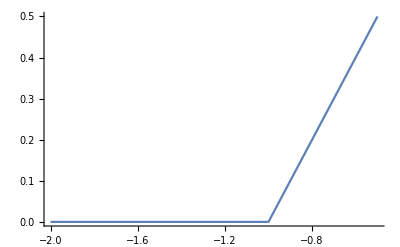

```mathematica
Plot[SmoothedTrapez[x,1,1,1*10^(-13)],{x,-2,2},PlotRange->All]
```